# Feynrules_Example_phi4

```mathematica
$FeynRulesPath=SetDirectory["/Users/yifanchen/Library/Wolfram/Applications/FeynRules"];
```

```mathematica
<<FeynRules`
```

- FeynRules -

Version: 2.3.49 ( 29 September 2021).

Authors: A. Alloul, N. Christensen, C. Degrande, C. Duhr, B. Fuks

Please cite:

- Comput.Phys.Commun.185:2250-2300,2014 (arXiv:1310.1921);

- Comput.Phys.Commun.180:1614-1641,2009 (arXiv:0806.4194).

http://feynrules.phys.ucl.ac.be

The FeynRules palette can be opened using the command FRPalette[].

```mathematica
SetDirectory[$FeynRulesPath<>"/Models/Snu"];
```

```mathematica
LoadModel["Snu.fr"];
verts=FeynmanRules[Lscalar];
```

This model implementation was created by

YC

Model Version: 1.0

For more information, type ModelInformation[].

- Loading particle classes.

- Loading parameter classes.

Model ScalarModel loaded.

Starting Feynman rule calculation.

Expanding the Lagrangian...

Collecting the different structures that enter the vertex.

1 possible non-zero vertices have been found -> starting the computation:  / 1.

1 vertex obtained.

```mathematica
WriteFeynArtsOutput[Lscalar,Output->"ScalarModel_FA"];
```

- - - FeynRules interface to FeynArts - - -

C. Degrande C. Duhr, 2013

Counterterms: B. Fuks, 2012

Creating output directory: ScalarModel_FA

Calculating Feynman rules for L1

Starting Feynman rules calculation for L1.

Expanding the Lagrangian...

Collecting the different structures that enter the vertex.

1 possible non-zero vertices have been found -> starting the computation:  / 1.

1 vertex obtained.

mytimecheck,after LGC

Writing FeynArts model file into directory ScalarModel_FA

Writing FeynArts generic file on ScalarModel_FA.gen.

# Feynrules_Example_eN_axion_Snu

```mathematica
Quit[]
Clear["Global`*"];
```

```mathematica
$FeynRulesPath=SetDirectory["/Users/xuliang/opt/feynrules-current"];
<<FeynRules`
```

- FeynRules -

Version: 2.3.49 ( 29 September 2021).

Authors: A. Alloul, N. Christensen, C. Degrande, C. Duhr, B. Fuks

Please cite:

- Comput.Phys.Commun.185:2250-2300,2014 (arXiv:1310.1921);

- Comput.Phys.Commun.180:1614-1641,2009 (arXiv:0806.4194).

http://feynrules.phys.ucl.ac.be

The FeynRules palette can be opened using the command FRPalette[].

```mathematica
SetDirectory[$FeynRulesPath<>"/Models"];
LoadModel["NNbrem_axion_Snu/NNbrem_axion_Snu.fr"];
verts=FeynmanRules[LQED];
```

This model implementation was created by

YC

XZ

Model Version: 0.1

For more information, type ModelInformation[].

- Loading particle classes.

- Loading gauge group classes.

- Loading parameter classes.

Model DF loaded.

Starting Feynman rule calculation.

Expanding the Lagrangian...

Collecting the different structures that enter the vertex.

5 possible non-zero vertices have been found -> starting the computation:  / 5.

5 vertices obtained.

```mathematica
vertsAll=FeynmanRules[LQED,FlavorExpand->True,ScreenOutput->True];
Cases[vertsAll,Vertex[{__F,__F,__V},___]->__]//Short
```

Starting Feynman rule calculation.

Expanding the Lagrangian...

Collecting the different structures that enter the vertex.

9 possible non-zero vertices have been found -> starting the computation:  / 9.

9 vertices obtained.

(* * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * *)

Vertex 1

Particle 1 : Dirac , e^-

Particle 2 : Dirac , e

Particle 3 : Scalar , s1

Vertex:

ⅈ ee (γ_(s_1,s_2))^5

(* * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * *)

Vertex 2

Particle 1 : Dirac , mu^-

Particle 2 : Dirac , mu

Particle 3 : Scalar , s1

Vertex:

ⅈ ee (γ_(s_1,s_2))^5

(* * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * *)

Vertex 3

Particle 1 : Dirac , ta^-

Particle 2 : Dirac , ta

Particle 3 : Scalar , s1

Vertex:

ⅈ ee (γ_(s_1,s_2))^5

(* * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * *)

Vertex 4

Particle 1 : Dirac , e^-

Particle 2 : Dirac , e

Particle 3 : Vector , A

Vertex:

ⅈ ee (γ_(s_1,s_2))^μ_3

(* * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * *)

Vertex 5

Particle 1 : Dirac , mu^-

Particle 2 : Dirac , mu

Particle 3 : Vector , A

Vertex:

ⅈ ee (γ_(s_1,s_2))^μ_3

(* * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * *)

Vertex 6

Particle 1 : Dirac , ta^-

Particle 2 : Dirac , ta

Particle 3 : Vector , A

Vertex:

ⅈ ee (γ_(s_1,s_2))^μ_3

(* * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * *)

Vertex 7

Particle 1 : Dirac , Proton^-

Particle 2 : Dirac , Proton

Particle 3 : Vector , A

Vertex:

ⅈ ee (γ_(s_1,s_2))^μ_3

(* * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * *)

Vertex 8

Particle 1 : Dirac , Nu^-

Particle 2 : Dirac , Snu

Particle 3 : Vector , A

Vertex:

-ⅈ muNuN (γ^μ_3.SlashedP[3])_(s_1,s_2)+ⅈ muNuN (SlashedP[3].γ^μ_3)_(s_1,s_2)

(* * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * *)

Vertex 9

Particle 1 : Dirac , Snu^-

Particle 2 : Dirac , Nu

Particle 3 : Vector , A

Vertex:

-ⅈ muNuN (γ^μ_3.SlashedP[3])_(s_1,s_2)+ⅈ muNuN (SlashedP[3].γ^μ_3)_(s_1,s_2)

(* * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * * *)

{}

```mathematica
$CurrentPath=SetDirectory[NotebookDirectory[]];
WriteFeynArtsOutput[LQED,Output->"NNbrem_axion_Snu_FA"];
```

- - - FeynRules interface to FeynArts - - -

C. Degrande C. Duhr, 2013

Counterterms: B. Fuks, 2012

Calculating Feynman rules for L1

Starting Feynman rules calculation for L1.

Expanding the Lagrangian...

Collecting the different structures that enter the vertex.

5 possible non-zero vertices have been found -> starting the computation:  / 5.

5 vertices obtained.

mytimecheck,after LGC

Writing FeynArts model file into directory NNbrem_axion_Snu_FA

Writing FeynArts generic file on NNbrem_axion_Snu_FA.gen.

```mathematica
WriteUFO[LQED];
```

--- Universal FeynRules Output (UFO) v 1.1 ---

Starting Feynman rule calculation.

Expanding the Lagrangian...

Collecting the different structures that enter the vertex.

5 possible non-zero vertices have been found -> starting the computation:  / 5.

5 vertices obtained.

Flavor expansion of the vertices:  / 5

- Saved vertices in InterfaceRun[ 1 ].

Computing the squared matrix elements relevant for the 1->2 decays:

/ 5

Squared matrix elent compute in 0.031613 seconds.

Decay widths computed in 0.000709 seconds.

Preparing Python output.

- Splitting vertices into building blocks.

Splitting of vertices distributed over 9 kernels.

- Optimizing: /9 .

- Writing files.

Done!

# FeyncalcInstall

```mathematica
Import["https://raw.githubusercontent.com/FeynCalc/feyncalc/master/install.m"];
InstallFeynCalc[]
```

Welcome to the automatic FeynCalc installer brought to you by the FeynCalc developer team!

• To install the current stable version of FeynCalc (recommended for productive use), please evaluate

InstallFeynCalc[]

• To install the development version of FeynCalc (only for experts or beta testers), please evaluate

InstallFeynCalc[InstallFeynCalcDevelopmentVersion->True]

Downloading FeynCalc from https://github.com/FeynCalc/feyncalc/archive/hotfix-stable.zip ...done! 
FeynCalc zip file was saved to /private/var/folders/kb/5zph_vd96d12pb8hs5f5hzrw0000gn/T/m000005620771.
Extracting FeynCalc zip file to /private/var/folders/kb/5zph_vd96d12pb8hs5f5hzrw0000gn/T/m000005620771.dir ...done! 
Checking the directory structure...done! 
Copying FeynCalc to /Users/yifanchen/Library/Wolfram/Applications/FeynCalc ...done! 
Setting up the format type of new output cells ... done! 
Creating the configuration file ... done! 
Downloading FeynArts from https://github.com/FeynCalc/feynarts-mirror/archive/master.zip ...done! 
FeynArts zip file was saved to /private/var/folders/kb/5zph_vd96d12pb8hs5f5hzrw0000gn/T/m000006620771.
Extracting FeynArts zip file to /Users/yifanchen/Library/Wolfram/Applications/FeynCalc/FeynArts ...done! 
Copying FeynArts to /Users/yifanchen/Library/Wolfram/Applications/FeynCalc/FeynArts ...done! 

Installation complete! Loading FeynCalc ... 
Successfully patched FeynArts.

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

# FeynCalc_Example_phi4

```mathematica
Quit[]
```

```mathematica
If[ $FrontEnd === Null,$FeynCalcStartupMessages = False;Print[description];];
If[ $Notebooks === False,$FeynCalcStartupMessages = False];
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose = 0;
FCCheckVersion[9,3,1];
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
SetOptions[InsertFields,Model->"/Users/yifanchen/FeynRules/Models/Snu/ScalarModel_FA/ScalarModel_FA"];
```

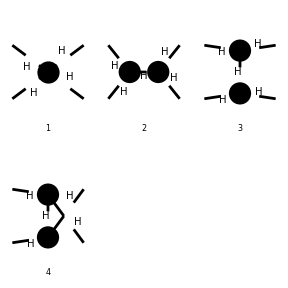

FeynArtsGraphics({H,H}→{H,H})(([1] | [2] | [3]
[4] | Null | Null
Null | Null | Null))

```mathematica
top=CreateTopologies[0,2->2];
ins=InsertFields[top,{S[1],S[1]}->{S[1], S[1]},InsertionLevel->{Classes}];
Paint[ins,Numbering->Simple,PaintLevel->{Classes}]
ampFA=CreateFeynAmp[ins];
```

```mathematica
amp=FCFAConvert[ampFA,IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},LoopMomenta->{},ChangeDimension->4]//Contract//Simplify
```

{-(3 (FCGV(EL))^2 (FCGV(MH))^2)/(4 (FCGV(MW))^2 (FCGV(SW))^2),-(9 (FCGV(EL))^2 (FCGV(MH))^4)/(4 (FCGV(MW))^2 (FCGV(SW))^2 ((OverBar[p3]+OverBar[p4])^2-(FCGV(MH))^2)),-(9 (FCGV(EL))^2 (FCGV(MH))^4)/(4 (FCGV(MW))^2 (FCGV(SW))^2 ((OverBar[p4]-OverBar[p2])^2-(FCGV(MH))^2)),-(9 (FCGV(EL))^2 (FCGV(MH))^4)/(4 (FCGV(MW))^2 (FCGV(SW))^2 ((OverBar[p3]-OverBar[p2])^2-(FCGV(MH))^2))}

```mathematica
Msq=Simplify[amp*ComplexExpand[Conjugate[amp]]];
s=SP[p1+p2,p1+p2];
dsdo=Msq/(128 Pi^2 s);
sigmaTot=4 Pi dsdo//Simplify;

Print["M = ",amp];
Print["|M|^2 = ",Msq];
Print["dσ/dΩ (CM, identical finals) = ",dsdo];
Print["σ_total (CM, identical finals) = ",sigmaTot];
```

M = {-(3 (FCGV(EL))^2 (FCGV(MH))^2)/(4 (FCGV(MW))^2 (FCGV(SW))^2),-(9 (FCGV(EL))^2 (FCGV(MH))^4)/(4 (FCGV(MW))^2 (FCGV(SW))^2 ((OverBar[p3]+OverBar[p4])^2-(FCGV(MH))^2)),-(9 (FCGV(EL))^2 (FCGV(MH))^4)/(4 (FCGV(MW))^2 (FCGV(SW))^2 ((OverBar[p4]-OverBar[p2])^2-(FCGV(MH))^2)),-(9 (FCGV(EL))^2 (FCGV(MH))^4)/(4 (FCGV(MW))^2 (FCGV(SW))^2 ((OverBar[p3]-OverBar[p2])^2-(FCGV(MH))^2))}

|M|^2 = {(9 (FCGV(EL))^4 (FCGV(MH))^4)/(16 (FCGV(MW))^4 (FCGV(SW))^4),(81 (FCGV(EL))^4 (FCGV(MH))^8 (1/((OverBar[p3]+OverBar[p4])^2-(FCGV(MH))^2))^2)/(16 (FCGV(MW))^4 (FCGV(SW))^4),(81 (FCGV(EL))^4 (FCGV(MH))^8 (1/((OverBar[p4]-OverBar[p2])^2-(FCGV(MH))^2))^2)/(16 (FCGV(MW))^4 (FCGV(SW))^4),(81 (FCGV(EL))^4 (FCGV(MH))^8 (1/((OverBar[p3]-OverBar[p2])^2-(FCGV(MH))^2))^2)/(16 (FCGV(MW))^4 (FCGV(SW))^4)}

dσ/dΩ (CM, identical finals) = {(9 (FCGV(EL))^4 (FCGV(MH))^4)/(2048 π^2 (FCGV(MW))^4 (FCGV(SW))^4 (OverBar[p1]+OverBar[p2])^2),(81 (FCGV(EL))^4 (FCGV(MH))^8 (1/((OverBar[p3]+OverBar[p4])^2-(FCGV(MH))^2))^2)/(2048 π^2 (FCGV(MW))^4 (FCGV(SW))^4 (OverBar[p1]+OverBar[p2])^2),(81 (FCGV(EL))^4 (FCGV(MH))^8 (1/((OverBar[p4]-OverBar[p2])^2-(FCGV(MH))^2))^2)/(2048 π^2 (FCGV(MW))^4 (FCGV(SW))^4 (OverBar[p1]+OverBar[p2])^2),(81 (FCGV(EL))^4 (FCGV(MH))^8 (1/((OverBar[p3]-OverBar[p2])^2-(FCGV(MH))^2))^2)/(2048 π^2 (FCGV(MW))^4 (FCGV(SW))^4 (OverBar[p1]+OverBar[p2])^2)}

σ_total (CM, identical finals) = {(9 (FCGV(EL))^4 (FCGV(MH))^4)/(512 π (FCGV(MW))^4 (FCGV(SW))^4 (OverBar[p1]+OverBar[p2])^2),(81 (FCGV(EL))^4 (FCGV(MH))^8 (1/((OverBar[p3]+OverBar[p4])^2-(FCGV(MH))^2))^2)/(512 π (FCGV(MW))^4 (FCGV(SW))^4 (OverBar[p1]+OverBar[p2])^2),(81 (FCGV(EL))^4 (FCGV(MH))^8 (1/((OverBar[p4]-OverBar[p2])^2-(FCGV(MH))^2))^2)/(512 π (FCGV(MW))^4 (FCGV(SW))^4 (OverBar[p1]+OverBar[p2])^2),(81 (FCGV(EL))^4 (FCGV(MH))^8 (1/((OverBar[p3]-OverBar[p2])^2-(FCGV(MH))^2))^2)/(512 π (FCGV(MW))^4 (FCGV(SW))^4 (OverBar[p1]+OverBar[p2])^2)}

# FeynCalc_Example_eN_axion

```mathematica
Quit[]
Clear["Global`*"];
```

```mathematica
If[ $FrontEnd === Null,$FeynCalcStartupMessages = False;Print[description];];
If[ $Notebooks === False,$FeynCalcStartupMessages = False];
$LoadAddOns={"FeynCalc"};
<<FeynCalc`
$FAVerbose = 0;
FCCheckVersion[9,3,1];
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

OpenRead::noopen: Cannot open /Users/xuliang/Library/Mathematica/Applications/FeynCalc/AddOns/FeynCalc/FeynCalc.m.

Get::noopen: Cannot open /Users/xuliang/Library/Mathematica/Applications/FeynCalc/AddOns/FeynCalc/FeynCalc.m.

```mathematica
SetOptions[InsertFields,Mod;
```

SetOptions::optnf: Model is not a known option for InsertFields.

```mathematica
diags=InsertFields[CreateTopologies[0,2->3,ExcludeTopologies->{WFCorrections}],{F[2,{1}],F[5]}->{F[2,{1}],F[5],S[1]},InsertionLevel->{Classes}];
Paint[diags,ColumnsXRows->{2,1},Numbering->Simple,ImageSize->{512,256}];
ampFA=CreateFeynAmp[diags];
```

-Graphics-

```mathematica
amp=FCFAConvert[ampFA,IncomingMomenta->{k1,p1},OutgoingMomenta->{k2,p2,q1},UndoChiralSplittings->True,ChangeDimension->4,List->False,SMP->True,Contract->True]//.{Momentum[Plus[Times[-1,k2],p1,Times[-1,p2]]]->Momentum[Plus[Times[-1,k1],q1]],Momentum[Plus[Times[-1,p1],p2]]->Momentum[Plus[Times[-1,k1],q1,k2]],Momentum[Plus[p1,Times[-1,p2]]]->Momentum[Plus[Times[-1,k1],q1,k2]],Momentum[Plus[k2,Times[-1,p1],p2]]->Momentum[Plus[k1,Times[-1,q1]]],MuD->0}
```

-(ⅈ gc2 gc3 (φ(OverBar[p2],Mn)).(γ̄)^Lor1.(φ(OverBar[p1],Mn)) (φ(OverBar[k2],ME)).(ⅈ gc1 (γ̄)^7-ⅈ gc1 (γ̄)^6).(γ̄·(OverBar[k2]+OverBar[q1])+ME).(γ̄)^Lor1.(φ(OverBar[k1],ME)))/((-OverBar[k1]+OverBar[k2]+OverBar[q1])^2 ((-OverBar[k2]-OverBar[q1])^2-ME^2))-(ⅈ gc2 gc3 (φ(OverBar[p2],Mn)).(γ̄)^Lor2.(φ(OverBar[p1],Mn)) (φ(OverBar[k2],ME)).(γ̄)^Lor2.(γ̄·(OverBar[k1]-OverBar[q1])+ME).(ⅈ gc1 (γ̄)^7-ⅈ gc1 (γ̄)^6).(φ(OverBar[k1],ME)))/((-OverBar[k1]+OverBar[k2]+OverBar[q1])^2 ((OverBar[q1]-OverBar[k1])^2-ME^2))

```mathematica
ampSquare[amp]=Simplify[DiracSimplify[(FermionSpinSum[#1,ExtraFactor->1/2^2]&)[FeynAmpDenominatorExplicit[amp*ComplexConjugate[amp]]]]];
```

```mathematica
basis2={Pair[Momentum[k1],Momentum[p2]]->(ME+Dot[OverBar[k1],OverBar[k1]]/(2ME))(Mn+Dot[OverBar[p2],OverBar[p2]]/(2Mn))-Dot[OverBar[k1],OverBar[p2]],Pair[Momentum[p1],Momentum[k2]]->(ME+Dot[OverBar[k2],OverBar[k2]]/(2ME))(Mn+Dot[OverBar[p1],OverBar[p1]]/(2Mn))-Dot[OverBar[k2],OverBar[p1]],Pair[Momentum[p1],Momentum[p2]]->(Mn+Dot[OverBar[p1],OverBar[p1]]/(2Mn))(Mn+Dot[OverBar[p2],OverBar[p2]]/(2Mn))-Dot[OverBar[p1],OverBar[p2]],Pair[Momentum[p1],Momentum[q1]]->(Mn+Dot[OverBar[p1],OverBar[p1]]/(2Mn))Subscript[q, 0]-Dot[OverBar[p1],q̄],Pair[Momentum[p2],Momentum[q1]]->(Mn+Dot[OverBar[p2],OverBar[p2]]/(2Mn)) Subscript[q, 0]-Dot[OverBar[p2],q̄],Pair[Momentum[k2],Momentum[k1]]->(ME+Dot[OverBar[k1],OverBar[k1]]/(2ME))(ME+Dot[OverBar[k2],OverBar[k2]]/(2ME))-Dot[OverBar[k1],OverBar[k2]],Pair[Momentum[p1],Momentum[k1]]->(ME+Dot[OverBar[k1],OverBar[k1]]/(2ME))(Mn+Dot[OverBar[p1],OverBar[p1]]/(2Mn))-Dot[OverBar[k1],OverBar[p1]],Pair[Momentum[q1],Momentum[k1]]->(ME+Dot[OverBar[k1],OverBar[k1]]/(2ME))Subscript[q, 0]-Dot[OverBar[k1],q̄],Pair[Momentum[p2],Momentum[k2]]->(ME+Dot[OverBar[k2],OverBar[k2]]/(2ME))(Mn+Dot[OverBar[p2],OverBar[p2]]/(2Mn)) -Dot[OverBar[k2],OverBar[p2]],Pair[Momentum[q1],Momentum[k2]]->(ME+Dot[OverBar[k2],OverBar[k2]]/(2ME)) Subscript[q, 0]-Dot[OverBar[k2],q̄]};
```

```mathematica
amptest=ampSquare[amp]//.basis2//.{Pair[Momentum[k1],Momentum[k1]]|Pair[Momentum[k2],Momentum[k2]]->ME^2,Pair[Momentum[p1],Momentum[p1]]|Pair[Momentum[p2],Momentum[p2]]->Mn^2,Pair[Momentum[q1],Momentum[q1]]->Mdr^2,Subscript[q, 0]->√(Mdr^2+Dot[q̄,q̄])}//.Mdr->0;
```

```mathematica
Series[Series[amptest,{Mn,Infinity,-2}],{ME,Infinity,2}]//.{OverBar[k1]->ū+OverBar[k2]}//.Dotr//Simplify
```

Mn^2 ((4 gc1^2 gc2^2 gc3^2 (q̄.q̄ ū.ū-(ū.q̄)^2))/(q̄.q̄ (ū.(2 q̄-ū))^2 ME^2)+O((1/ME)^3))+O(1/(1/Mn))

# FeynCalc_Example _eN _Snu

```mathematica
Quit[]
```

```mathematica
If[ $FrontEnd === Null,$FeynCalcStartupMessages = False;Print[description];];
If[ $Notebooks === False,$FeynCalcStartupMessages = False];
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose = 0;
FCCheckVersion[9,3,1];
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
diags=InsertFields[CreateTopologies[0,2->4,ExcludeTopologies->{WFCorrections}],{F[2,{1}],F[5]}->{F[2,{1}],F[5],F[1],F[6]},InsertionLevel->{Classes},Model->FileNameJoin[{"/Users/yifanchen/Library/Wolfram/Applications/FeynRules/Models/NNbrem_axion_Snu/NNbrem_axion_Snu_FA","NNbrem_axion_Snu_FA"}]];
Paint[diags,Numbering->Simple,ImageSize->{512,256}]
```

InitializeModel::incomp1: Coupling definition in model file for C[-F(1),F(6),V(1)] is incompatible to generic coupling structure.  Coupling is not a vector of length 2.

$Aborted

Paint(diags,Numbering→Simple,ImageSize→{512,256})